```mathematica
SetDirectory["/home/etuxr/spring20/comphys/week10/report"];
```

## Problem 2

```mathematica
data=ReadList["!./laplace 100 1e-10 | awk '/^temp/{print $2, $3, $4}'",{Number,Number,Number}];
flux = ReadList["!./laplace 100 1e-10 | awk '/^flux/{print $2, $3, $4}'",{Number,Number}]
```

{{1245.76,1245.76}}

```mathematica
ListContourPlot[data,Contours->{320,360,400,440,480},ContourLabels->All,Epilog->Rectangle[{-5,-5},{5,5}]]
```

-Graphics-

```mathematica
datae=ReadList["!./laplace 100 1e-10 | awk '/^grad/{print $2, $3, $4, $5}'",{Number,Number,Number,Number}];
```

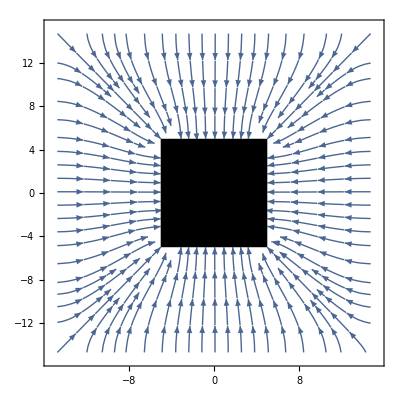

```mathematica
ListStreamPlot[datae,RegionFunction->Function[{x,y},Abs[x]>5||Abs[y]>5],Epilog->Rectangle[{-5,-5},{5,5}],VectorScale->0.06]
```

## Problem 3

```mathematica
datae=Table[Flatten[{n*12+1,ReadList["!./laplace "<> ToString[n*12+1] <>" 1e-10 | awk '/^iterations/{print $2, $3, $4, $5}'", Number]}],{n, 5,20}];
```

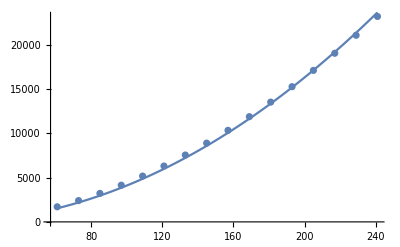

```mathematica
dots=ListPlot[datae];
f=Fit[datae,{1+x+x^2}, x];
line=Plot[f,{x,12*5+1, 12*20+1}];
Show[dots,line]
```

## Problem 4

```mathematica
datae=Table[Flatten[{1/n*12+1,ReadList["!./laplace "<> ToString[n*12+1] <>" 1e-10 | awk '/^flux/{print $2}'", Number]}],{n, 5,20}];
```

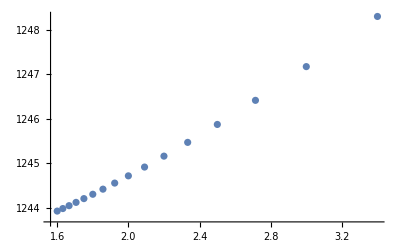

```mathematica
ListPlot[datae]
```